## Brian — PS 3 — 2025-01-24 — Solution

## Exercises from EIWL3 Section 9

```mathematica
(* 9.1 *) Manipulate[Range[n],{n,0,100,1}]
```

```mathematica
(* 9.2 *) Manipulate[NumberLinePlot[Range[n]],{n,5,50,1}]
```

```mathematica
(* 9.3 *) Manipulate[Column[Table[x,n]],{n,1,10,1}]
```

```mathematica
(* 9.4 *) Manipulate[Graphics[Style[Disk[],Hue[hue]]],{hue,0,1}]
```

```mathematica
(* 9.5 *) Manipulate[Graphics[Style[Disk[],RGBColor[r, g, b]]],{r,0,1},{g,0,1},{b,0,1}]
```

```mathematica
(* 9.6 *) Manipulate[IntegerDigits[n],{n,1000,9999,1}]
```

```mathematica
(* 9.7 *) Manipulate[Table[Hue[i/(n-1)],{i,0,n-1}],{n,5,50}] (* Perhaps I got a bit carried away with my interpretation of equally-spaced :) *)
```

```mathematica
(* 9.8 *) Manipulate[Table[Graphics[Style[RegularPolygon[6],Hue[hue]]],count],{count,1,10,1},{hue,0,1}]
```

```mathematica
(* 9.9 *) Manipulate[Graphics[Style[RegularPolygon[count],color]],{count,5,20,1},{color,{Red,Green,Blue}}]
```

```mathematica
(* 9.10 *) Manipulate[PieChart[Table[1,n]],{n,1,10}]
```

```mathematica
(* 9.11 *) Manipulate[BarChart[IntegerDigits[n]],{n,100,999,1}]
```

```mathematica
(* 9.12 *) Manipulate[Table[RandomColor[],n],{n,1,50}]
```

```mathematica
(* 9.13 *) Manipulate[Column[Table[base^exponent,{base,1,25}]],{exponent,1,10,1}]
```

```mathematica
(* 9.14 *) Manipulate[NumberLinePlot[Range[10]^exponent],{exponent,0,5,1}]
```

```mathematica
(* 9.15 *) Manipulate[Graphics3D[Style[Sphere[],RGBColor[1-redToGreen,redToGreen,0]]],{redToGreen,0,1}]
```

## Exercises from EIWL3 Section 10

```mathematica
anImage=CurrentImage[]; (* An image I will be re-using for lots of the exercises *)
```

```mathematica
(* 10.1 *) ColorNegate[anImage]
```

-Graphics-

```mathematica
(* 10.2 *) Manipulate[Blur[anImage,blur],{blur,0,20}]
```

```mathematica
(* 10.3 *) Table[EdgeDetect[Blur[anImage,blur]],{blur,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 10.4 *) ImageCollage[{anImage,Blur[anImage],EdgeDetect[anImage],Binarize[anImage]}]
```

-Graphics-

```mathematica
(* 10.5 *) anImage+Binarize[anImage]
```

-Graphics-

```mathematica
(* 10.6 *) Manipulate[EdgeDetect[Blur[anImage,blur]],{blur,0,20}]
```

```mathematica
(* 10.7 *) EdgeDetect[Graphics3D[Sphere[]]]
```

-Graphics-

```mathematica
(* 10.8 *) Manipulate[Blur[Graphics[Style[RegularPolygon[5],Purple]],blur],{blur,0,20}]
```

```mathematica
(* 10.9 *) ImageCollage[
Table[
Graphics[Style[Disk[],RandomColor[]]],
{i,1,9}]
]
```

-Graphics-

```mathematica
(* 10.10 *) ImageCollage[
Table[
Graphics3D[Style[Sphere[],Hue[hue]]],
{hue,0.0,1.0,0.2}]
]
```

-Graphics-

```mathematica
(* 10.11 *) Table[
Blur[Graphics[Disk[]],blur],
{blur,0,30,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 10.12 *) ImageAdd[anImage,Graphics[Disk[]]]
```

-Graphics-

```mathematica
(* 10.13 *) ImageAdd[anImage,Graphics[Style[RegularPolygon[8],Red]]]
```

-Graphics-

```mathematica
(* 10.14 *) ImageAdd[anImage,ColorNegate[EdgeDetect[anImage]]]
```

-Graphics-

## Exercises 11.1-11.15 from EIWL3 Section 11

```mathematica
(* 11.1 *) StringJoin[Table["Hello",2]]
```

HelloHello

```mathematica
(* 11.2 *) ToUpperCase[StringJoin[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
(* 11.3 *) StringJoin[Reverse[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
(* 11.4 *) StringJoin[Reverse[Alphabet[]]]
```

zyxwvutsrqponmlkjihgfedcba

```mathematica
(* 11.5 *) StringTake[StringJoin[Alphabet[]],6]
```

abcdef

```mathematica
(* 11.6 *) (* I had to look up a solution for this, mostly because I did not understand the question. *)
Column[Table[StringTake["this is about strings",n],{n,StringLength["this is about strings"]}]]
```

t
th
thi
this
this 
this i
this is
this is 
this is a
this is ab
this is abo
this is abou
this is about
this is about 
this is about s
this is about st
this is about str
this is about stri
this is about strin
this is about string
this is about strings

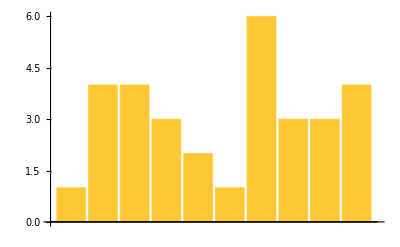

```mathematica
(* 11.7*) BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away"]]]
```

```mathematica
(* 11.8 *)StringLength[WikipediaData["Computer"]]
```

60266

```mathematica
(* 11.9 *)Length[TextWords[WikipediaData["Computer"]]]
```

9271

```mathematica
(* 11.10 *) First[TextSentences[WikipediaData["Computer"]]]
```

A computer is a machine that can be programmed to automatically carry out sequences of arithmetic or logical operations (computation).

```mathematica
(* 11.11 *) StringJoin[StringTake[TextSentences[WikipediaData["Computer"]],1]]
```

AMTTACCESEMTTTCTPP=ITTDBTTTT==DTLTTTSITIIDMTTAAATTTIASIBIAITITIITSI=CCAHTFTTTAEBNH=ITax()2{,THI=DHTTTTAB==CBTDETTITIRTZTT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAATBAIL=TJFCJTHATHTTWITT=TTDTKIHKNNHPNIMTGFTTWISTITS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIETWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCICW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITTSTTITMWITC=PUTTS=MF=ATHHIT=PALTP=ETHOBSA=CTITTITCITA"=AWA=TMH=TQCVSLTTT=ACARPE=AT=====M

```mathematica
(* 11.12 *) Last[SortBy[WordList[],StringLength]]
(* I learned while grading that using Max is better than what I did *)
```

electroencephalographic

```mathematica
(* 11.13 *) (* I had to look up a solution for this, but now that I see it, I should have had it on my own. *)
Count[StringTake[WordList[],1],"q"]
```

194

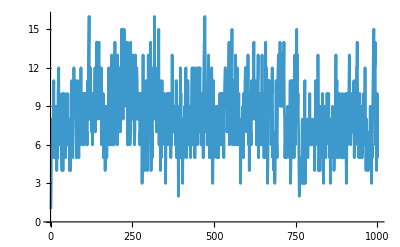

```mathematica
(* 11.14 *)ListLinePlot[StringLength[Take[WordList[],1000]]]
```

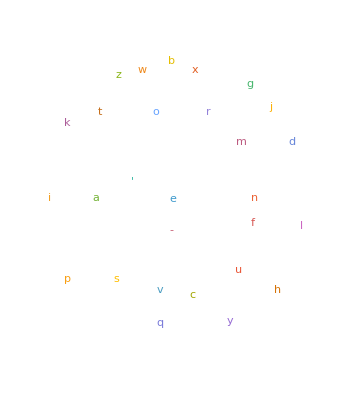

```mathematica
(* 11.15 *) WordCloud[Characters[StringJoin[WordList[]]]]
```